Capturing packets from a Network Interface

Ramesh Nikhil

Johnson Ian

BITS Pilani, India.

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: The aim of the project was to add support for capturing network packets on any particular interface to Mathematica. The functions should aid in debugging network problems and capturing packets which use TCP and UDP protocols.The idea is to create a new function which then invokes a c++ library in the background which starts sniffing packets. Based on the "time"and  "protocol"  variable set in the function parameter the library returns the packet data to Mathematica which can then be used to make inferences, plot graphs which in turn can be used in help in debugging network issues.

SUMMARY OF WORK: Functions which print out TCP, UDP, DNS data were added on the Mathematica side which use the “libtins” C++ library on the backend. The entire TCP/UDP packet is serialized and sent to Mathematica where it’s parsed. Fields returned inside Source/Destination IP/Port, Checksum, Length, Headersize, ack, timestamp etc.

RESULTS AND FUTURE  WORK: The same work can be extended to make it function real time where we are able to visualize the traffic in Mathematica.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

Packet Sniffing
	New Mathematica Function
	Backend C++ Library -> Libtins
	LibraryLink Interface
	Support for TCP/UDP
	Network Debugging
Check response times for requests to a particular domain, a particular ip or even a particular port. With Mathematica’s advance plotting features it’s very easy to visualise the erroneous packet.

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Functions which print out TCP, UDP, DNS data were added on the Mathematica side which use the "libtins" C++ library on the backend. The entire TCP/UDP packet is serialized and sent to Mathematica where it's parsed. Fields returned inside Source/Destination IP/Port, Checksum, Length, Headersize, ack ,timestamp etc.

Code

https://github.com/rnikhil275/wolfram-2017

Written Content / Lesson Plans

Conclusions in Detail

The added functions can be used to capture and analyze network data for TCP and UDP protocols in near real time.

All Visualizations

Time vs Destination IP’s

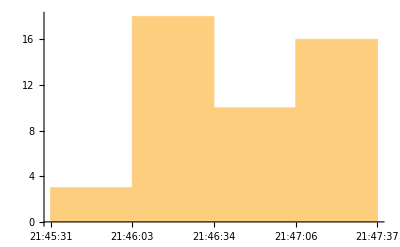

Source IP vs Payload

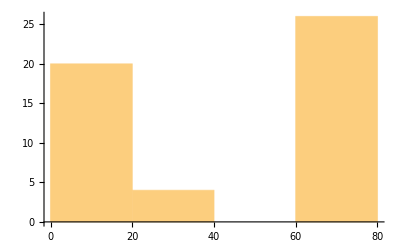

Data Sources Links/References

Future Directions

Make the functions real time so that Mathematica can capture and analyze packets on the fly.

Background Info Links/References

Libtins

Keywords

Provide keywords as items

packet capture

libtins

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```